```mathematica
IceData= Import["Desktop\\icebern.dat"];
Length[IceData]
```

1096

Tukey Windowing:  The values of ω and λ can be determined by allowing M=59,  (where 59 is approx. 2√854 where 854 is the number of observed values in the second periodic series).  (Note that matrixes will only accumulate to M-1 in order to avoid λ_59 =0 appearing in matrix.)   As per p. 133, ω_j= (π*j)/m nd λ_k=1/2(1+cos((π*k)/m)).  ω and λ are calculated below. 

As follows, using autocovariance (ck) values and using (eq 7.21):    πf̂(ω_j)- λ_0 c_0= 2*∑_(k=1)^m c_k λ_k Cos[ω_jk],  I will calculate fhat.

```mathematica
k=1;{};
omega={};
lambda={};
While[k≤58,
λ=1/2*(1.+Cos[(Pi*k)/59.]);
AppendTo[lambda,λ];
ω=(Pi*k)/59.;
AppendTo[omega,ω];
k++
];
omega[[1]]
```

0.0532473

As follows, I will calculate all autocovariance values:

```mathematica
mean=Mean[IceData[[2]]];
autolist={};
nn=1;
While[nn≤1096,
autoco=∑_(k=1)^(1096-nn) ((IceData[[k]][[2]]-mean)*(IceData[[(k+nn)]][[2]]-mean))/1096;

AppendTo[autolist,autoco];
nn++
];
autolist
```

{2387.65,2368.31,2344.8,2323.61,2299.86,2277.38,2253.16,2230.05,2206.22,2182.78,2160.63,2139.52,2117.42,2097.28,2076.54,2058.53,2041.05,2023.21,2002.7,1982.65,1962.87,1943.3,1925.9,1908.12,1890.79,1874.06,1856.32,1839.83,1821.96,1806.46,1790.19,1775.07,1760.46,1747.84,1735.57,1723.03,1711.12,1698.7,1687.24,1676.66,1666.92,1656.71,1647.22,1638.98,1630.75,1621.87,1613.29,1605.16,1599.45,1592.64,1587.15,1582.87,1579.41,1578.19,1576.64,1574.56,1572.99,1571.8,1567.87,1565.58,1563.95,1564.37,1563.51,1565.2,1567.75,1572.47,1578.,1584.62,1590.,1595.78,1599.61,1604.18,1606.78,1609.5,1611.97,1612.65,1612.93,1614.31,1616.04,1618.94,1620.01,1621.73,1622.58,1625.06,1627.85,1632.76,1637.18,1640.38,1643.06,1644.84,1648.67,1650.29,1652.42,1653.81,1654.66,1654.18,1654.23,1654.72,1654.12,1653.17,1651.1,1649.76,1648.78,1648.35,1645.79,1642.09,1639.22,1636.28,1634.3,1633.09,1632.22,1630.39,1628.32,1625.46,1623.04,1620.65,1617.99,1614.54,1611.1,1607.39,1604.39,1602.3,1601.58,1601.07,1602.2,1603.05,1603.52,1602.11,1600.31,1598.51,1595.25,1592.74,1590.45,1587.98,1584.76,1582.26,1578.55,1574.95,1571.31,1569.23,1566.27,1563.42,1559.7,1554.35,1548.82,1540.87,1532.3,1524.41,1516.24,1506.77,1497.56,1488.96,1482.59,1475.89,1468.27,1461.05,1453.54,1447.93,1442.07,1436.59,1432.54,1428.93,1426.22,1421.56,1417.38,1414.93,1413.07,1410.2,1409.01,1408.94,1408.52,1407.15,1405.9,1404.22,1402.53,1400.69,1400.84,1401.14,1402.53,1404.18,1404.5,1405.02,1404.95,1405.47,1406.07,1406.14,1406.85,1405.85,1405.,1401.77,1400.38,1397.31,1395.1,1390.36,1386.75,1380.29,1376.36,1373.4,1371.83,1369.12,1366.91,1363.7,1361.94,1360.31,1360.27,1358.34,1357.76,1354.99,1352.92,1351.31,1350.98,1349.91,1349.37,1347.42,1346.14,1345.3,1345.42,1344.72,1344.87,1345.97,1346.48,1344.97,1343.16,1339.93,1336.93,1332.36,1327.9,1324.33,1319.84,1313.34,1307.48,1299.62,1291.87,1284.13,1276.27,1267.06,1257.69,1249.55,1240.81,1232.78,1223.96,1216.34,1209.58,1203.78,1199.84,1196.53,1194.37,1191.26,1190.86,1189.18,1187.24,1184.9,1183.91,1182.49,1182.17,1183.76,1186.14,1189.42,1191.92,1192.8,1194.9,1196.18,1197.29,1196.64,1197.42,1198.86,1200.64,1202.83,1204.13,1205.6,1207.21,1208.56,1210.51,1213.11,1215.8,1218.31,1220.69,1221.45,1224.01,1224.4,1225.59,1225.87,1225.92,1226.58,1226.68,1226.8,1226.29,1224.89,1222.34,1219.67,1216.56,1212.05,1208.12,1201.55,1193.93,1186.01,1178.4,1170.48,1161.38,1151.01,1140.25,1131.2,1123.61,1117.28,1111.05,1104.78,1098.84,1091.39,1084.32,1079.26,1075.15,1071.29,1065.98,1062.32,1059.4,1056.11,1051.38,1046.03,1040.76,1037.06,1033.34,1029.95,1027.9,1026.33,1025.56,1023.7,1023.05,1022.13,1019.94,1016.55,1014.5,1011.89,1008.62,1004.48,1000.18,995.875,991.774,987.557,983.621,979.077,974.402,970.065,966.776,963.527,960.779,957.752,956.234,954.251,953.647,951.71,949.697,947.64,946.332,946.052,946.311,946.769,948.045,949.944,953.33,957.068,963.013,969.626,976.278,981.599,986.423,989.934,992.152,994.547,995.962,996.401,996.878,997.66,998.128,997.922,996.732,996.06,995.341,995.981,998.176,1001.14,1004.44,1008.26,1011.62,1015.74,1020.2,1025.77,1030.89,1036.14,1041.42,1046.26,1051.06,1056.02,1060.4,1064.63,1067.73,1070.82,1073.36,1077.28,1080.71,1083.26,1085.41,1088.49,1091.7,1095.,1097.34,1099.42,1099.84,1100.23,1100.2,1099.65,1098.58,1097.41,1095.65,1093.43,1090.51,1087.96,1085.85,1083.76,1081.53,1079.36,1076.65,1073.44,1069.95,1066.69,1062.9,1059.51,1055.66,1051.86,1048.99,1046.14,1043.11,1039.55,1036.19,1032.31,1026.96,1021.93,1016.57,1011.23,1004.92,999.142,992.624,985.722,978.315,970.737,962.982,955.826,949.388,943.248,936.254,930.796,924.92,919.379,913.123,907.925,903.057,899.333,896.102,892.432,888.863,886.317,883.561,880.757,878.228,876.577,874.641,873.182,872.438,871.316,870.614,869.24,866.963,864.833,863.882,863.277,862.083,861.175,859.481,858.273,856.913,855.12,853.034,850.578,848.653,846.244,845.099,844.131,842.661,841.515,840.486,841.261,843.03,845.57,847.741,850.797,854.916,859.841,865.3,870.873,876.29,879.726,883.032,885.76,887.979,890.612,892.965,895.294,897.44,898.85,899.272,898.63,896.591,894.459,892.416,891.193,889.673,888.307,886.055,883.417,880.034,876.865,873.727,870.801,867.089,863.547,860.383,857.415,854.61,851.89,848.698,845.343,841.671,837.841,833.362,829.905,825.27,819.901,814.24,809.238,804.009,800.764,798.582,796.824,795.78,795.812,796.344,796.714,797.709,799.414,801.031,802.954,804.777,807.312,809.712,812.199,814.882,817.289,819.152,820.577,821.475,821.55,821.097,821.312,820.883,819.556,817.407,815.691,814.988,814.598,814.118,813.391,812.145,810.669,810.823,812.12,812.307,812.194,811.356,811.98,811.208,809.996,807.374,805.478,805.164,805.528,805.454,805.797,805.889,805.16,805.615,805.45,805.576,804.725,803.114,800.311,797.377,795.072,792.087,786.642,781.323,776.104,772.198,767.795,764.764,760.97,756.885,751.369,745.662,740.002,735.136,732.934,730.063,726.452,723.02,720.148,717.904,715.752,714.349,712.905,712.828,712.497,712.001,711.422,711.068,711.299,711.556,711.66,712.578,713.81,714.329,715.262,715.653,716.934,716.81,716.876,717.131,717.843,718.165,720.272,721.365,723.475,726.035,729.855,731.429,734.706,737.758,741.147,744.041,746.595,749.574,751.77,753.27,754.825,756.269,758.75,762.142,765.137,767.6,770.068,772.137,774.238,776.244,777.271,777.952,777.601,777.084,775.732,774.132,772.681,771.791,771.723,772.352,774.121,775.544,777.295,778.986,780.496,782.193,783.951,785.041,785.141,784.457,783.48,781.975,780.372,778.716,776.945,775.03,773.333,770.461,769.192,766.981,764.191,761.433,760.483,757.961,757.653,755.679,753.54,750.207,747.305,742.955,738.238,732.437,725.87,718.583,711.301,703.578,696.775,688.387,681.161,674.409,668.214,662.406,657.677,652.806,649.494,647.636,646.41,644.667,642.471,639.666,636.026,632.501,628.565,624.477,621.483,619.086,616.469,615.171,612.383,609.853,605.961,601.933,597.191,593.398,589.563,585.851,580.119,573.182,565.918,559.682,552.99,547.181,541.123,536.703,532.498,528.19,524.018,519.821,514.818,510.191,505.881,502.779,499.84,498.272,495.532,493.336,490.545,487.13,483.466,479.831,476.975,474.026,471.011,468.163,466.067,464.01,461.599,458.894,456.098,453.675,451.996,451.573,451.819,452.355,453.311,453.447,454.568,454.654,454.885,455.802,455.851,456.395,457.371,458.299,458.137,457.723,457.185,456.918,458.12,459.17,459.84,458.985,457.549,456.248,455.388,454.857,454.866,454.902,453.87,452.96,452.318,451.691,451.255,450.674,449.258,446.88,444.823,443.629,441.401,439.518,438.392,437.2,435.655,434.868,434.201,433.168,431.665,429.944,428.216,426.538,424.607,423.201,421.558,420.042,417.987,415.85,412.506,408.873,404.574,399.915,395.134,390.519,385.202,381.227,377.13,373.199,369.163,365.848,362.376,359.826,356.415,353.655,350.749,349.217,348.106,346.595,344.544,342.475,340.08,336.693,333.107,329.795,326.967,324.169,321.124,318.037,314.26,310.853,307.94,305.908,303.553,301.676,299.255,297.448,296.154,294.148,291.962,290.566,289.585,287.746,286.697,285.474,283.566,280.988,277.611,274.032,270.765,266.748,262.935,259.345,255.078,251.614,248.358,245.086,240.588,236.316,231.748,229.223,227.223,225.418,222.674,219.719,216.721,214.665,212.168,208.286,204.083,200.112,197.384,195.852,192.306,190.404,187.996,184.175,180.59,178.744,176.867,174.969,172.102,169.123,166.428,163.388,160.066,156.754,153.43,150.136,147.187,144.348,141.605,139.657,137.074,134.49,131.888,129.067,126.271,123.087,120.192,116.97,113.558,109.883,106.294,102.736,98.9458,95.2126,91.733,88.0316,84.747,81.1264,77.905,74.5227,71.6986,69.2203,66.7342,64.2731,61.9953,59.6925,57.4427,55.2262,53.167,50.9975,49.7206,48.2422,46.8132,45.325,43.6203,41.8279,40.1083,38.2819,36.4052,34.1024,32.1181,30.0001,28.0594,26.2617,24.655,22.9816,21.1537,19.7742,18.2548,16.6034,14.9345,13.4831,11.9166,10.5638,9.55121,8.46112,7.85452,7.07831,6.29463,5.64444,5.00305,4.29402,3.5743,2.95697,2.39129,1.89622,1.41986,1.20789,0.795926,0.438894,0.163417,-0.0846419,-0.438321,-0.683615,-1.12488,-1.57725,-1.74106,-1.86013,-1.94525,-2.11226,-2.22978,-2.3754,-2.15642,-2.06251,-1.89003,-1.87348,-2.05127,-2.17686,-2.17541,-2.30414,-2.20553,-2.17272,-2.12126,-2.11205,-2.27234,-2.31383,-2.26631,-2.3198,-2.34615,-2.48285,-2.47224,-2.63839,-2.72515,-2.56893,-2.6293,-3.03966,-3.51303,-3.68318,-3.81758,-4.2727,-4.66774,-5.01506,-5.24036,-5.39114,-5.46944,-5.46768,-5.88102,-5.98108,-6.17907,-6.23378,-6.5688,-6.81841,-6.94102,-6.97336,-6.95389,-6.93248,-6.73446,-6.67435,-6.73491,-6.80557,-6.89607,-6.88124,-6.88136,-6.90357,-6.94443,-6.80076,-6.62421,-6.68511,-6.70138,-6.65211,-6.58131,-6.5365,-6.68558,-6.62844,-6.63824,-6.64021,-6.71417,-6.7774,-6.49981,-6.65898,-6.48891,-6.3913,-6.35808,-6.41462,-6.4669,-6.46545,-6.35448,-6.24888,-6.09489,-6.01854,-5.89254,-5.74394,-5.57099,-5.32021,-5.09627,-4.79404,-4.34036,-3.66883,-3.00953,-2.65859,-1.93154,-1.40572,-0.931432,-0.656959,0}

Here, I will interpolate to find the m=59 autocovariance( ck) values (to be used below to find fhat)

```mathematica
amplist={};
autolist2={};
nk=1;
While[nk≤58,
autocount=autolist[[Round[(nk*(1096-242))/59.+242]]];
amptude=autocount*lambda[[nk]];
AppendTo[amplist,amptude];
AppendTo[autolist2,autocount];
nk++
];
autolist2
```

{1183.76,1207.21,1226.68,1151.01,1062.32,1019.94,966.776,949.944,997.66,1030.89,1085.41,1087.96,1046.14,962.982,888.863,863.277,841.515,887.979,886.055,841.671,796.714,821.55,812.307,805.615,760.97,712.905,716.81,744.041,777.271,780.496,766.981,718.583,642.471,597.191,519.821,474.026,454.568,459.84,446.88,426.538,381.227,340.08,299.255,266.748,219.719,176.867,137.074,88.0316,50.9975,24.655,6.29463,-0.683615,-2.17686,-2.72515,-5.88102,-6.88124,-6.64021,-5.89254}

In order to acquire the approximated Tukey value, I will use eqn 7.21 ( f̂(ω)= 1/π{λ_0 c_0+2*∑_(k=1)^m λ_k c_k Cos[ω_jk]).

```mathematica
zero=∑_(k=1)^1096 ((IceData[[k]][[2]]-mean)*(IceData[[(k)]][[2]]-mean))/1096;
f[w_]=1/Pi*(zero+2*∑_(k=1)^58 amplist[[k]]*Cos[w*k]);
flist={};
mm=1;
While[mm≤58,
fhat=f[omega[[mm]]];
AppendTo[flist,fhat];
mm++
];
flist//MatrixForm
```

(10829.
2442.94
694.929
935.668
510.043
425.5
616.918
805.169
706.169
650.649
769.267
581.983
193.86
71.1655
148.03
130.262
141.219
303.752
445.552
464.131
373.364
264.245
269.672
362.065
403.152
379.947
356.016
346.984
363.574
399.673
415.068
404.383
393.951
392.88
395.256
411.857
451.355
465.78
433.322
405.968
404.901
410.676
412.989
410.446
395.863
370.853
364.342
376.5
375.888
368.805
383.56
415.078
423.374
399.607
379.891
371.204
368.441
388.425)

```mathematica
fhattime={};
cktime={};
ckomega={};
fhatomega={};
mk=1;
While[mk≤58,
yearint=IceData[[Round[(mk*(1096-242))/59.+242]]][[1]];
AppendTo[fhattime,{yearint,flist[[mk]]}];
AppendTo[fhatomega,{omega[[mk]],flist[[mk]]}];
AppendTo[ckomega,{omega[[mk]],autolist2[[mk]]}];
AppendTo[cktime,{yearint,autolist2[[mk]]}];
mk++
];
ckomega//MatrixForm
```

(0.0532473 | 1183.76
0.106495 | 1207.21
0.159742 | 1226.68
0.212989 | 1151.01
0.266237 | 1062.32
0.319484 | 1019.94
0.372731 | 966.776
0.425979 | 949.944
0.479226 | 997.66
0.532473 | 1030.89
0.585721 | 1085.41
0.638968 | 1087.96
0.692215 | 1046.14
0.745463 | 962.982
0.79871 | 888.863
0.851957 | 863.277
0.905205 | 841.515
0.958452 | 887.979
1.0117 | 886.055
1.06495 | 841.671
1.11819 | 796.714
1.17144 | 821.55
1.22469 | 812.307
1.27794 | 805.615
1.33118 | 760.97
1.38443 | 712.905
1.43768 | 716.81
1.49093 | 744.041
1.54417 | 777.271
1.59742 | 780.496
1.65067 | 766.981
1.70391 | 718.583
1.75716 | 642.471
1.81041 | 597.191
1.86366 | 519.821
1.9169 | 474.026
1.97015 | 454.568
2.0234 | 459.84
2.07665 | 446.88
2.12989 | 426.538
2.18314 | 381.227
2.23639 | 340.08
2.28964 | 299.255
2.34288 | 266.748
2.39613 | 219.719
2.44938 | 176.867
2.50262 | 137.074
2.55587 | 88.0316
2.60912 | 50.9975
2.66237 | 24.655
2.71561 | 6.29463
2.76886 | -0.683615
2.82211 | -2.17686
2.87536 | -2.72515
2.9286 | -5.88102
2.98185 | -6.88124
3.0351 | -6.64021
3.08835 | -5.89254)

```mathematica
SecondPSeries=Take[IceData,{243,1096}];
Print["Fhat Values Overlayed with Observational Data vs. Age"]
ListLinePlot[{SecondPSeries,fhattime},PlotLegends->Automatic,PlotMarkers->Automatic,AxesLabel->{Age,Co2},PlotRange->{0,1200}]
Print["Fhat Values Overlayed with Autocorrelation Values vs. Frequency"]
ListLinePlot[{ckomega,fhatomega},PlotLegends->Automatic,PlotMarkers->Automatic,AxesLabel->{Frequency,Co2}]
Print["Fhat Values Overlayed with Autocorrelation Values vs. Age"]
ListLinePlot[{cktime,fhattime},PlotLegends->Automatic,PlotMarkers->Automatic,AxesLabel->{Age,Co2}]
Print["CkValues Data vs. K"];
ListLinePlot[autolist2,PlotLegends->Automatic,PlotMarkers->Automatic,AxesLabel->{Age,Co2}];
Print["Amplitude vs. K"];
ListLinePlot[amplist,PlotLegends->Automatic,PlotMarkers->Automatic,AxesLabel->{Age,Co2}];
```

Fhat Values Overlayed with Observational Data vs. Age

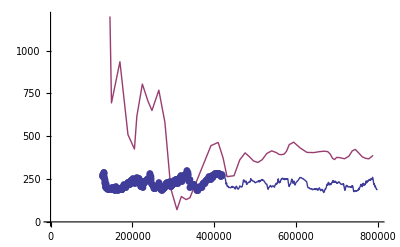

Fhat Values Overlayed with Autocorrelation Values vs. Frequency

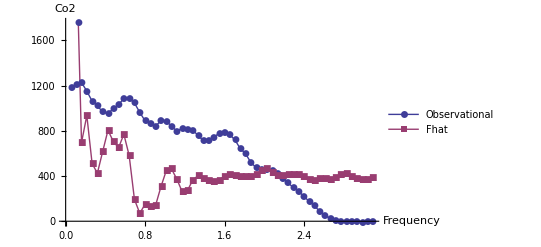

Fhat Values Overlayed with Autocorrelation Values vs. Age

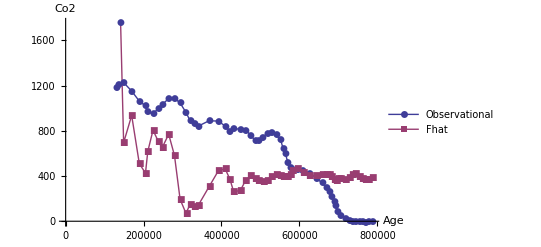

CkValues Data vs. K

Amplitude vs. K